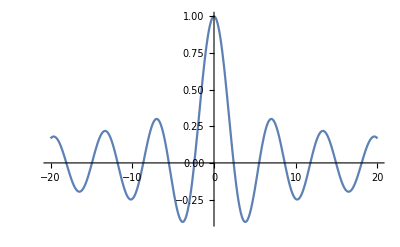

```mathematica
Plot[BesselJ[0,x],{x,-20,20}]
```

```mathematica
Sort[DeleteDuplicates[x/.Table[FindRoot[BesselJ[0,x],{x,i}],{i,1,10}]]]
```

{-52.6241,2.40483,5.52008,5.52008,8.65373}

Solutions of the Bessel equation of order zero (J0(x))can be seen as above. One can find the radial modes of vibration of such a drum by seeting x=ru, and thus the modes of vibrations would have the form J0(ur). r=1, at the rim, and j0(u)=0 initially, when it is still. Thus the zeroes of J0(x) give the frequencies of radial vibrations of a circular drum. The first two fundamental frequencies will be 2.404 and 5.52

The smallest associated frequency of vibration is the smallest zero of the J0 bessel function so it can be described as Bessel[0,2.4*r]*Cos[2.4t] for the first one

```mathematica
Manipulate[{GraphicsRow[{
ParametricPlot3D[{r*Cos[x],r*Sin[x],BesselJ[0,2.404825557695773*r]*Cos[2.4048*t]},{x,0,2Pi},{r,0,1},PlotRange->{-1,1},ImageSize->Medium,ViewPoint->Front],Plot[BesselJ[0,2.4048*r]Cos[2.4048t],{r,-1,1},PlotRange->{-1,1},ImageSize->Medium]}]},{t,0.00001,10}]
```

Given initial conditions of r0=1 and t0=2Pi

```mathematica
Manipulate[{GraphicsRow[{
ParametricPlot3D[{r*Cos[x],r*Sin[x],BesselJ[0,2.404825557695773*r]*Sin[2Pi*t]},{x,0,2Pi},{r,0,1},PlotRange->{-1,1},ImageSize->Medium,ViewPoint->Front],Plot[BesselJ[0,2.4048*r]Sin[2Pi*t],{r,-1,1},PlotRange->{-1,1},ImageSize->Medium]}]},{t,0.00001,10}]
```

Second frequency

```mathematica
Graphics3D[{Opacity[.3],Cylinder[]}]
```

-Graphics3D-

```mathematica
Manipulate[{GraphicsRow[{
Show[ParametricPlot3D[{r*Cos[x],r*Sin[x],BesselJ[0,5.520078110286309*r]*Sin[2*Pi*t]},{x,0,2Pi},{r,0,1},PlotRange->{-1,1},ImageSize->Medium,ViewPoint->Front],Graphics3D[{Opacity[.3],Cylinder[{{0,0,0},{0,0,-1}},1]}]],Plot[BesselJ[0,5.520078110286309*r]Sin[2*Pi*t],{r,-1,1},PlotRange->{-1,1},ImageSize->Medium]}]},{t,0.00001,10}]
```